{a→Function[{t},-ⅇ^(t/9)],b→Function[{t},ⅇ^(1-Cos[t])]}

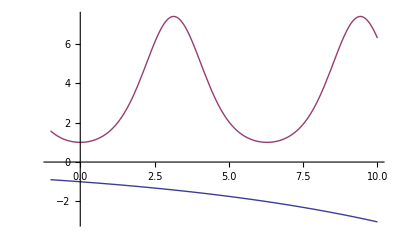

```mathematica
sol=DSolve[{a'[t]==a[t]/9,b'[t]==Sin[t]*b[t],a[0]==-1,b[0]==1},{a,b},t]//FullSimplify//Flatten
Plot[Evaluate[{a[t],b[t]}/.sol],{t,0,10},WorkingPrecision->20]
```